Testing Spatial Audio on a Single Plane - 2D

## Determining Delay with Dist. to Ears

Graphical Visualization

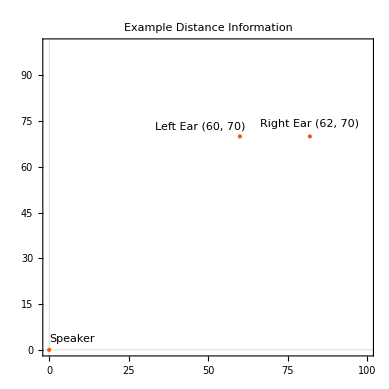

```mathematica
ListPlot[{
Labeled[{0,0},"Speaker"],
Labeled[{60,70}, "Left Ear (60, 70)"],
Labeled[{82,70}, "Right Ear (62, 70)"]
},
PlotTheme->"Scientific",
PlotRange->{{0,100},{0,100}},
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Example Distance Information"]
```

Assigning Attributes

```mathematica
distanceLeftEar = Quantity[√(60.^2+70.^2),"centimeters"]
distanceRightEar = Quantity[√(62.^2+70.^2), "centimeters"]
(*Angle Between Speaker and X-axis when connected as Right Triangle with Ear*)
thetaLeftEar =Quantity[ArcTan[70./60.] ,"radians"]
thetaRightEar =Quantity[ArcTan[70./62.], "radians"]
```

92.1954 cm

93.5094 cm

0.86217 rad

0.84593 rad

Speed of Sound

```mathematica
speedOfSound =StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"]
```

340.29 m/s

Determining Delays

```mathematica
delayLeftEar=distanceLeftEar/speedOfSound
delayRightEar = distanceRightEar / speedOfSound
```

0.00270932 s

0.00274793 s

## Working with Audio Functions to Channel Delay

```mathematica
sampleAudio=Import["/Users/shubhamkumar/Downloads/prenks/Serene Queen - LDR.mp3"]
```

```mathematica
(*Doesn't Work, Stereo not split into Mono for each Channel*)
AudioChannelSeparate[sampleAudio]
```

{,}

Visualizing Audio and Trimming For Faster Processing

-Graphics-

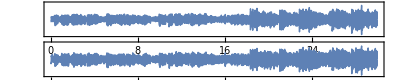

2

```mathematica
sampleAudioTrimmed = AudioTrim[sampleAudio, {10,40}]
Spectrogram[sampleAudioTrimmed]
AudioPlot[sampleAudioTrimmed]
AudioChannels[sampleAudioTrimmed]
```

Panning Test

```mathematica
leftAudio = AudioPan[sampleAudioTrimmed,-1.]
rightAudio = AudioPan[sampleAudioTrimmed, 1.]
```

```mathematica
AudioChannelCombine[{leftAudio, rightAudio}]
```

Delaying Audio For Each Channel

```mathematica
delayedLeftAudio = AudioDelay[leftAudio,delayLeftEar]
delayedRightAudio= AudioDelay[rightAudio,delayRightEar]
(*Making Sure Delay Worked*)
Duration@delayedLeftAudio
Duration@leftAudio
Duration@delayedRightAudio
Duration@rightAudio
```

30.0027 s

30. s

30.0027 s

30. s

```mathematica
AudioChannelCombine[{delayedRightAudio, delayedLeftAudio}]
```

## GUI Implementation